# Load packages

```mathematica
SetDirectory[NotebookDirectory[]<>"../package/"];
Get["funcs_rxns_moms_NEW.m"]
Needs["diffTVR`"]
```

```mathematica
?diffTVR`*
```

# Import

## Import cache

```mathematica
nv=2;
nh=1;

volExp=14;
noIP3R=100;
cdir=getCacheDirRaw[volExp,noIP3R];
SetDirectory[NotebookDirectory[]];
dataDesc=importDataDesc[cdir<>"data_desc.txt"];
```

```mathematica
SetDirectory[NotebookDirectory[]];

ip3s={"ip3_0p100","ip3_0p200","ip3_0p300","ip3_0p400","ip3_0p500","ip3_0p600","ip3_0p700","ip3_0p800","ip3_0p900","ip3_1p000","ip3_1p100","ip3_1p200","ip3_1p300","ip3_1p400","ip3_1p500","ip3_1p600","ip3_1p700","ip3_1p800","ip3_1p900","ip3_2p000"};

params0=Association[];
Do[
pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"params0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

params0[ip3]=makePStructFromLFDL[nv,nh,pLFDL];
,{ip3,ip3s}];
```

## Calculate derivs0

```mathematica
tvrDiff[nv_,nh_,ip3sTVR_,params_,dataDesc_]:=Module[
{alphas,dx,n,structsTVR,noOptSteps,derivs,ip3,dat,derivGuess,iIP3}
,
alphas=<|
"wt11"->100,(*100,*)
"wt12"->5000,
"sig2"->5000,
"b1"->100,(*100,*)
"b2"->100
|>;

dx=1;
n=dataDesc["noTpts"];
structsTVR=makeTVRstructs[n,dx,alphas["wt11"]];

noOptSteps=10;
derivs=Association[];

Monitor[
Do[
ip3=ip3sTVR[[iIP3]];
derivs[ip3]=Association[];
derivs[ip3]["LFDL"]=Association[];

Do[
dat=params[ip3]["LFDL"][k];

If[k!="varh11"&&k!="muh1",

structsTVR["alpha"]=alphas[k];
derivGuess=ConstantArray[0,n-1];
derivs[ip3]["LFDL"][k]=getDiffTVRGivenStructs[dat,derivGuess,noOptSteps,structsTVR];

,

derivs[ip3]["LFDL"][k]=deriv[dat];

];
,{k,makeLF[nv,nh]}];

derivs[ip3]=makePStructFromLFDL[nv,nh,derivs[ip3]["LFDL"]];
,{iIP3,Length[ip3sTVR]}];
,ProgressIndicator[iIP3,{1,Length[ip3sTVR]}]];

Return[{derivs,structsTVR}];
]
```

```mathematica
makeFilteredFromDerivs[nv_,nh_,ip3sTVR_,derivs_,params_,structsTVR_]:=Module[
{filtered,initPt}
,
filtered=Association[];
Do[
filtered[ip3]=Association[];
filtered[ip3]["LFDL"]=Association[];

Do[
If[k=="sig2",initPt=1.5*10^-6];
If[k=="b2",initPt=Mean[params[ip3]["LFDL"][k]]];
If[k=="wt12",initPt=0.00005];
If[k!="sig2"&&k!="b2"&&k!="wt12",initPt=params[ip3]["LFDL"][k][[1]];];
filtered[ip3]["LFDL"][k]=initPt+structsTVR["amat"].derivs[ip3]["LFDL"][k];
filtered[ip3]["LFDL"][k]=Flatten[{initPt,filtered[ip3]["LFDL"][k]}];
,{k,makeLF[nv,nh]}];

filtered[ip3]=makePStructFromLFDL[nv,nh,filtered[ip3]["LFDL"]];
,{ip3,ip3sTVR}];

Return[filtered]
]
```

```mathematica
{derivs,structsTVR}=tvrDiff[nv,nh,ip3s,params0,dataDesc];
```

```mathematica
derivsPRE=derivs;
```

```mathematica
(* Make small derivatives = 0 *)
magZero=10^-5;
derivs=Association[];
Do[
derivs[ip3]=Association[];
Do[
If[k=="b2"||k=="wt12"||k=="sig2",
derivs[ip3][k]=Table[0.0,{x,derivsPRE[ip3]["LFDL"][k]}],
derivs[ip3][k]=Table[If[Abs[x]<magZero,0.0,x],{x,derivsPRE[ip3]["LFDL"][k]}]
]
,{k,makeLF[nv,nh]}];

derivs[ip3]=makePStructFromLFDL[nv,nh,derivs[ip3]];
,{ip3,Keys[derivsPRE]}]
```

```mathematica
filtered=makeFilteredFromDerivs[nv,nh,ip3s,derivs,params0,structsTVR];
```

```mathematica
momentsFilteredTrue=Association[];
Do[
momentsFilteredTrueLD=Table[convertParamsToMoments[nv,x],{x,filtered[ip3]["LD"]}];
momentsFilteredTrue[ip3]=makeMStructFromLD[nv,nh,momentsFilteredTrueLD];
,{ip3,ip3s}];
```

```mathematica
momentsTrue=Association[];
Do[
momentsTrueLD=Table[convertParamsToMoments[nv,x],{x,params0[ip3]["LD"]}];
momentsTrue[ip3]=makeMStructFromLD[nv,nh,momentsTrueLD];
,{ip3,ip3s}];
```

```mathematica
pltEvery=10;
timesPlt=dataDesc["times"][[;;;;pltEvery]];
colors=Table[ColorData["BrownCyanTones"][i/Length[ip3s]],{i,Length[ip3s]}]
```

{RGBColor[0.4328202, 0.2875746, 0.16778140000000002],RGBColor[0.5179634, 0.3752862, 0.2504938],RGBColor[0.5943548, 0.45806840000000004, 0.33588],RGBColor[0.6619944, 0.5359212, 0.42394],RGBColor[0.729634, 0.613774, 0.512],RGBColor[0.7668376, 0.6736248, 0.5867076],RGBColor[0.8040412, 0.7334756, 0.6614152],RGBColor[0.8253242000000001, 0.787301, 0.7308212],RGBColor[0.8306866, 0.835101, 0.7949256],RGBColor[0.836049, 0.882901, 0.85903],RGBColor[0.8065450000000001, 0.9053942, 0.8961547999999999],RGBColor[0.777041, 0.9278874, 0.9332796],RGBColor[0.7376514, 0.9364448, 0.9557662],RGBColor[0.6883762, 0.9310664, 0.9636146],RGBColor[0.639101, 0.925688, 0.971463],RGBColor[0.585357, 0.8967528, 0.9580974],RGBColor[0.531613, 0.8678176000000001, 0.9447318],RGBColor[0.4723912, 0.8128028, 0.9049796],RGBColor[0.40769160000000004, 0.7317084, 0.8388408],RGBColor[0.342992, 0.650614, 0.772702]}

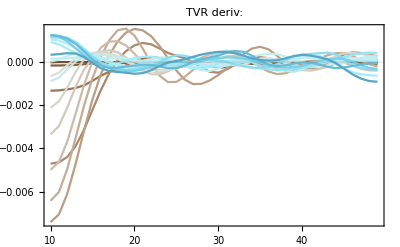
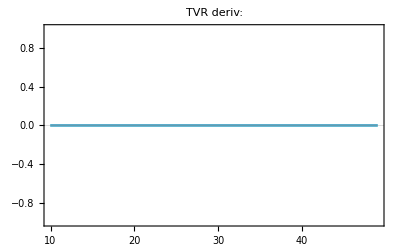
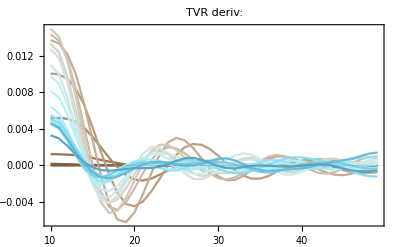
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0

```mathematica
plts=Table[
Show[
Table[
ip3=ip3s[[i]];
 xPlt=derivs[ip3]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt[[;;-2]],xPlt}],PlotRange->All,PlotStyle->colors[[i]]]
,{i,Length[ip3s]}],
PlotRange->All,
PlotLabel->"TVR deriv: "<>labels[k],
FrameLabel->{"Time (s)"}
]
,{k,makeLF[nv,nh]}];
p=Grid[ArrayReshape[plts,{3,3}]]
```

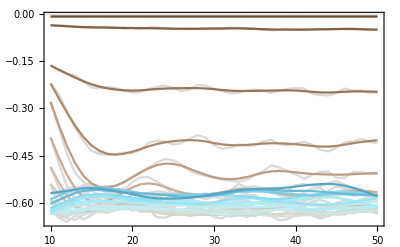
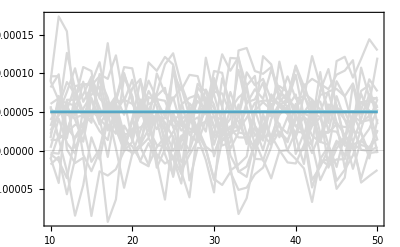
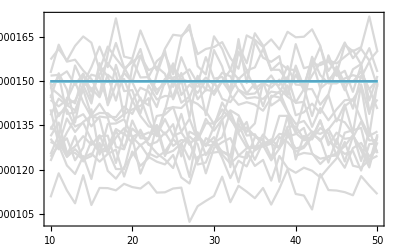
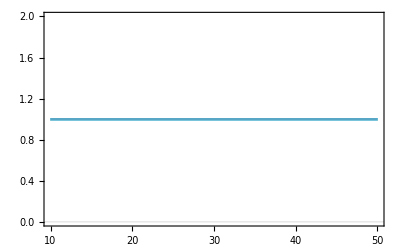
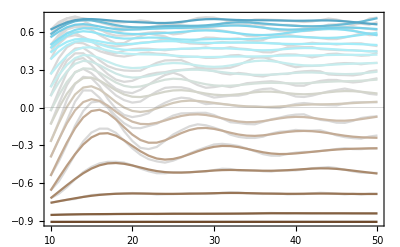
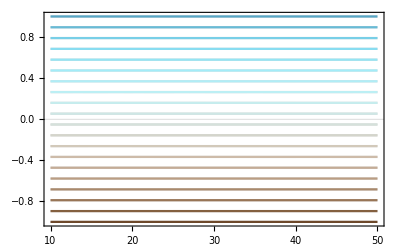
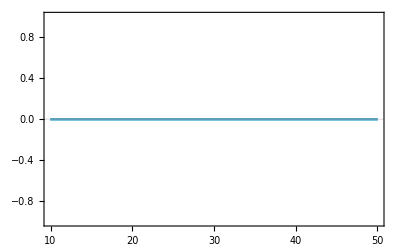
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0

```mathematica
plts=Table[
Show[
Table[
ip3=ip3s[[i]];
xPlt=params0[ip3]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt,xPlt}],PlotRange->All,PlotLabel->k,PlotStyle->LightGray]
,{i,Length[ip3s]}],
Table[
ip3=ip3s[[i]];
xPlt=filtered[ip3]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt,xPlt}],PlotRange->All,PlotLabel->k,PlotStyle->colors[[i]]]
,{i,Length[ip3s]}],
PlotRange->All,
PlotLabel->labels[k],
FrameLabel->{"Time (s)"}
]
,{k,makeLF[nv,nh]}];
p=Grid[ArrayReshape[plts,{3,3}]]
```

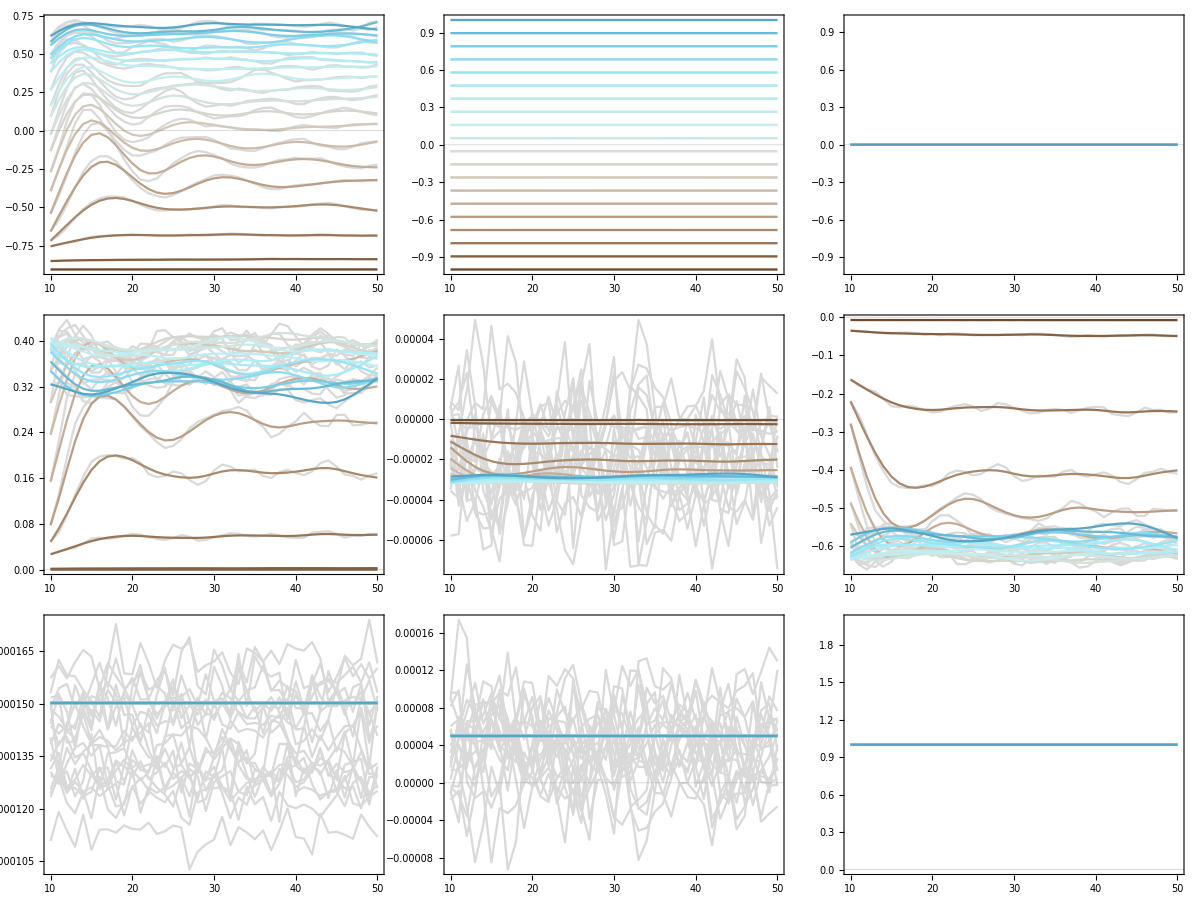

```mathematica
plts=Table[
Show[
Table[
ip3=ip3s[[i]];
xPlt=momentsTrue[ip3]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt,xPlt}],PlotRange->All,PlotLabel->k,PlotStyle->LightGray]
,{i,Length[ip3s]}],
Table[
ip3=ip3s[[i]];
xPlt=momentsFilteredTrue[ip3]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt,xPlt}],PlotRange->All,PlotLabel->k,PlotStyle->colors[[i]]]
,{i,Length[ip3s]}],
PlotRange->All,
PlotLabel->labels[k],
FrameLabel->{"Time (s)"}
]
,{k,makeLFM[nv,nh]}];
p=Grid[ArrayReshape[plts,{3,3}]]
```

## Export

```mathematica
exportToCache[nv_,nh_,params_,dataDesc_,subdir_]:=Module[
{x,cdir}
,
cdir=getCacheDir[dataDesc,noIP3R]<>subdir;
SetDirectory[NotebookDirectory[]];

Do[

If[!DirectoryQ[cdir<>ip3],CreateDirectory[cdir<>ip3]];
Do[
x=params[ip3]["LFDL"][k];
Export[cdir<>ip3<>"/"<>k<>".txt",StringRiffle[ToString[#,FortranForm]&/@PaddedForm[#,16]&/@x,"\n"]]
,{k,makeLF[nv,nh]}];

,{ip3,Keys[params]}];
]
```

```mathematica
noToStr[x_]:=StringReplace[ToString[PaddedForm[x,{3,1}]],{"."->"p","-"->"m"," "->""}]
```

```mathematica
subdir="derivs0/";
exportToCache[nv,nh,derivs,dataDesc,subdir];

subdir="filtered0/";
exportToCache[nv,nh,filtered,dataDesc,subdir];
```